```mathematica
(* I do not currently have damping included, so any non-zero A makes ω obtain an imaginary part! *)
```

```mathematica
g=980;
σ=72;
ρ=1;
k0=2*Pi/4*1.0;
h0=2;
M2=3;
κ[k_, n_]:=k+n*k0;
mat2[k_,A_]:=Table[((g+σ/ρ*κ[k,n]^2)*κ[k,n])*Exp[-κ[k,n]*h0]*(BesselJ[m-n,-I*κ[k,n]*A]+1/2*A*BesselJ[m-n-1,-I*κ[k,n]*A]+1/2*A*BesselJ[m-n+1,-I*κ[k,n]*A])+((g+σ/ρ*κ[k,n]^2)*κ[k,n])*Exp[κ[k,n]*h0]*(-BesselJ[m-n,I*κ[k,n]*A]+1/2*A*BesselJ[m-n-1,I*κ[k,n]*A]+1/2*A*BesselJ[m-n+1,I*κ[k,n]*A]),{n,-M2,M2},{m,-M2,M2}]
mat3[k_,A_]:=-Table[Exp[-κ[k,n]*h0]*(BesselJ[m-n,-I*κ[k,n]*A]+1/2*A*BesselJ[m-n-1,-I*κ[k,n]*A]+1/2*A*BesselJ[m-n+1,-I*κ[k,n]*A])-Exp[κ[k,n]*h0]*(-BesselJ[m-n,I*κ[k,n]*A]+1/2*A*BesselJ[m-n-1,I*κ[k,n]*A]+1/2*A*BesselJ[m-n+1,I*κ[k,n]*A]),{n,-M2,M2},{m,-M2,M2}]
```

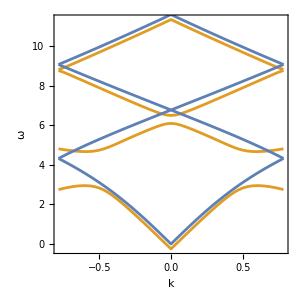

```mathematica
p1=ListPlot[Transpose[Table[{k,#/(2*Pi)}&/@(Re[Eigenvalues[{mat2[k,0.0],mat3[k,0.0]},-4]]^(1/2)),{k,-k0/2,k0/2,k0/50}]],Joined->True,Axes->False,Frame->True,FrameLabel->{k,ω},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,ImageSize->300,PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[1]]]];
p2=ListPlot[Transpose[Table[{k,#/(2*Pi)-0.25}&/@(Re[Eigenvalues[{mat2[k,1.75],mat3[k,1.75]},-4]]^(1/2)),{k,-k0/2,k0/2,k0/50}]],Joined->True,Axes->False,Frame->True,FrameLabel->{k,ω},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,ImageSize->300,PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[2]]]];
Show[p2,p1]
```